# Exercise 1

### Q1

```mathematica
q1exp1 = Expand[(1 + 3x +  b y)^5]
Factor[exp1]
```

1+15 x+90 x^2+270 x^3+405 x^4+243 x^5+5 b y+60 b x y+270 b x^2 y+540 b x^3 y+405 b x^4 y+10 b^2 y^2+90 b^2 x y^2+270 b^2 x^2 y^2+270 b^2 x^3 y^2+10 b^3 y^3+60 b^3 x y^3+90 b^3 x^2 y^3+5 b^4 y^4+15 b^4 x y^4+b^5 y^5

(1+3 x+b y)^5

### Q2

```mathematica
q2exp1 = Expand[(7x+8y)^8]
Coefficient[exp2,x^3]
```

5764801 x^8+52706752 x^7 y+210827008 x^6 y^2+481890304 x^5 y^3+688414720 x^4 y^4+629407744 x^3 y^5+359661568 x^2 y^6+117440512 x y^7+16777216 y^8

629407744 y^5

### Q3

```mathematica
q3int1 = Integrate[1/(5 x^2+1),x]
```

ArcTan[√5 x]/(√5)

### Q4

```mathematica
q4diff1 = D[q3int1, x]
```

1/(1+5 x^2)

### Q5

```mathematica
q5diff1 = D[x^(x^x), x]
```

x^(x^x) (x^(-1+x)+x^x Log[x] (1+Log[x]))

### Q6

```mathematica
q6aint1 = ∫_0^∞ Sin[a z]^2/z^2 ⅆz
```

ConditionalExpression[1/2 π Abs[a],a∈Reals]

```mathematica
q6bint1 = Integrate[(Sin[a z]^2) / (z^2),{z,0,Infinity}]
```

ConditionalExpression[1/2 π Abs[a],a∈Reals]

### Q7

```mathematica
q7aint1 = Integrate[E^(-3 x-x^4), x]
```

∫ⅇ^(-3 x-x^4)ⅆx

```mathematica
q7bint1 = Integrate[E^(-3 x-x^4),{x,0,Infinity}]
```

1/8 (8 Gamma[5/4] HypergeometricPFQ[{},{1/2,3/4},81/256]-6 √π HypergeometricPFQ[{},{3/4,5/4},81/256]+9 Gamma[3/4] HypergeometricPFQ[{},{5/4,3/2},81/256]-9 HypergeometricPFQ[{1},{5/4,3/2,7/4},81/256])

### Q8

```mathematica
x=.
```

```mathematica
q8exp1 = Normal[Series[(1 + x)^(0.5),{x,0,5}]]
```

1.+0.5 x-0.125 x^2+0.0625 x^3-0.0390625 x^4+0.0273438 x^5

```mathematica
q8exp2 = Normal[Series[(1 + x)^(0.5),{x,0,3}]]
```

1.+0.5 x-0.125 x^2+0.0625 x^3

```mathematica
x = 0.2
(1 + x)^(0.5)
q8exp1 
q8exp2
```

0.2

1.09545

1.09545

1.0955

### Q9

```mathematica
x=.
```

```mathematica
q9partial1 = Apart[(x-2)/(x^2 -1)]
```

-1/(2 (-1+x))+3/(2 (1+x))

### Q10

```mathematica
q10denominator1 = Factor[1+x^2,Extension->Sqrt[-1]]
```

(-ⅈ+x) (ⅈ+x)

```mathematica
q10partial1 = Apart[(x-2)/q10denominator1]
```

(1/2+ⅈ)/(-ⅈ+x)+(1/2-ⅈ)/(ⅈ+x)

### Q11

```mathematica
q11limit1 = Limit[Cot[x],x->π,Direction->1]
```

-∞

```mathematica
q11limit2 = Limit[Cot[x],x->π,Direction->-1]
```

∞

### Q12

```mathematica
q12limit1 = Limit[(1+p/n)^n,n->Infinity]
```

ⅇ^p

```mathematica
The distribution is Poission
```

### Q13

```mathematica
x=.
```

```mathematica
q13sol1 = Solve[x^6 == 1, x]
```

{{x→-1},{x→1},{x→-(-1)^(1/3)},{x→(-1)^(1/3)},{x→-(-1)^(2/3)},{x→(-1)^(2/3)}}

### Q14

```mathematica
x=.
```

```mathematica
q14eq1 = 3 x+5 y+d z==13 a
q14eq2 = 19 x+e y+29 z==37 b
q14eq3 = 43 x+47 y+f z==61 c
```

3 x+5 y+d z==13 a

19 x+e y+29 z==37 b

43 x+47 y+f z==61 c

```mathematica
q14sol1 = Solve[{q14eq1, q14eq2, q14eq3},{x,y, z}]
```

{{x→-(-17719 a+8845 c+1739 b d-61 c d e-185 b f+13 a e f)/(-2146-893 d+43 d e+95 f-3 e f),y→-(16211 a-5307 c-1591 b d+1159 c d-247 a f+111 b f)/(-2146-893 d+43 d e+95 f-3 e f),z→-(11609 a+2738 b-5795 c-559 a e+183 c e)/(-2146-893 d+43 d e+95 f-3 e f)}}

### Q15

```mathematica
x=.
```

```mathematica
q15deq1 = Tan[x] + D[y[x],x] == 1
```

Tan[x]+y'[x]==1

```mathematica
q15dsol1 = DSolve[q15deq1,y[x],x]
```

{{y[x]→x+C[1]+Log[Cos[x]]}}

### Q16

```mathematica
x=.
```

```mathematica
q16deq1 = D[y[x],x] + D[D[y[x],x],x] == 1-Sin[x]
```

y'[x]+y''[x]==1-Sin[x]

```mathematica
q16dsol1 = DSolve[{q16deq1, y[0] == 0.5, y'[0] == 1.5},y[x],x]
```

{{y[x]→1/2 (2 x+Cos[x]+Sin[x])}}

### Q17

```mathematica
x=.
```

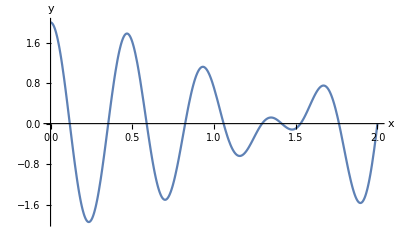

```mathematica
q17plot1 = Plot[(2-x^2)Cos[4.25 π x],{x,0,2}, AxesLabel->{"x", "y"}]
```